```mathematica
(*Data plot for lab 9*)
Needs["ErrorBarPlots`"]

(*tickSpecs correspond to elements: Iron, Selenium, Germanium, Cobalt, Manganese, Chromium, Vandium, Titanium*)
tickSpecs ={{{1,"Fe"},{2, "Se"},{3,"Ge"},{4,"Co"},{5,"Mg"},{6,"Cr"},{7, "V"},{8,"Ti"}},Automatic };

(*This data set correspond directly to the elements; these are energies in KeV, {energy,error}*)
dataEL={{6.325, 0.3},{10.983,0.3},{9.6411,0.3},{6.878,0.3},{5.852,0.3},{5.378,0.3},{4.904,0.3},{4.51,0.3}};
```

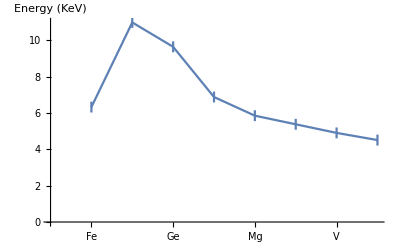

```mathematica
ErrorListPlot[dataEL,Joined->True,Frame->{Left,Bottom},Ticks->tickSpecs,AxesLabel->{None,Style["Energy (KeV)",12,FontFamily->"Arial"]}]
```